Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0.740741^ComplexInfinity encountered.

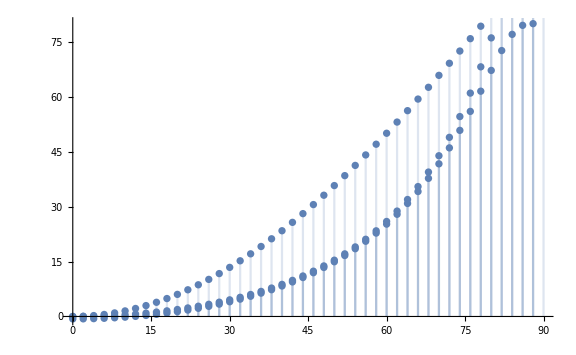

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0.740741^ComplexInfinity encountered.

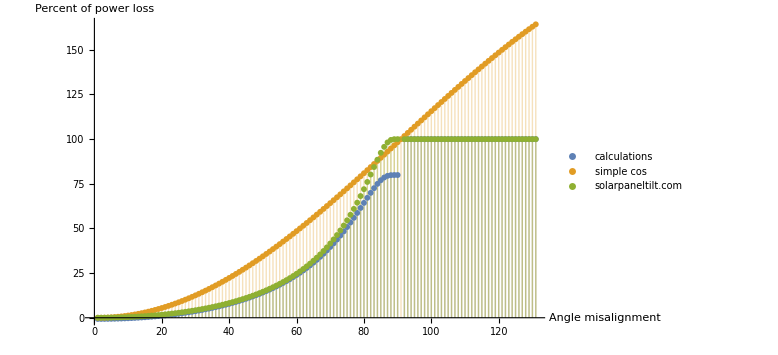

```mathematica
directPower  := Function[ (* param: hour of day*100, solar panel angle, date. returns W/m^2 *)
Subscript[θ, z]=#1; (* solar zenith (misalignment) in radians *)
n= QuantityMagnitude[Quantity[ DateObject[{2016,12,25}] - DateObject[{2016,1,1}]]];
Subscript[I, 0]= 1367 (1+0.034 Cos[360*n/365.25]);
Subscript[a, 0] = 0.4237 - 0.00821 36;
Subscript[a, 1] = 0.5055 + 0.00595 6.5^2;
k = 0.2711 + 0.01858 2.5^2;
If[Cos[Subscript[θ, z]]<0,
Subscript[I, direct]=0,
Subscript[I, direct] = Subscript[I, 0] (Subscript[a, 0] + Subscript[a, 1] E^(-k/Cos[Subscript[θ, z]])) (* If the sun is more than 90 degrees off, the formula is not correct, and we set the value to be 0 *)
]
]

directPowerPercent := Function[
(1-directPower[#1]/860)*100
]

solarPanelTilt[z_] := (
If[z>90,
100,
i =1.35*(1/1.35)^(Sec[z*Pi/180]);
(1-i)*100
]
)

(* DiscretePlot[1-Cos[x*Pi/180],{x,0,90,2},ImageSize->Large] *)

Show[DiscretePlot[directPowerPercent[x*Pi/180],{x,0,90,2},ImageSize->Large],
DiscretePlot[100*(1-Cos[x*Pi/180]),{x,0,90,2},ImageSize->Large],DiscretePlot[solarPanelTilt[x],{x,0,90,2},ImageSize->Large]
]

ListPlot[{Table[directPowerPercent[x*Pi/180],{x,0,130}],
Table[100*(1-Cos[x*Pi/180]),{x,0,130}],
Table[solarPanelTilt[x],{x,0,130}]},Filling -> Axis,PlotLegends -> {calculations,simple cos,solarpaneltilt.com},ImageSize -> Large,AxesLabel-> {"Angle misalignment","Percent of power loss"}]
```